```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY187/sec_int_data/610nm.dat"]
```

{{1.45287,0.258356},{1.39708,0.21188},{1.35876,0.175129},{1.32403,0.158797},{1.28662,0.150917},{1.25869,0.134618},{1.22636,0.135317},{1.19613,0.145312},{1.17366,0.136452},{1.15413,0.117516},{1.12528,0.0928526},{1.11495,0.14609},{1.10625,0.152464},{1.09912,0.170671},{1.09306,0.188386},{1.0888,0.201389},{1.08648,0.192849},{1.08572,0.178899},{1.08632,0.124428},{1.0888,0.113239},{1.09505,0.179735},{1.09559,0.194497},{1.12528,0.234202},{1.14263,0.261749},{1.16354,0.289905},{1.19414,0.299586},{1.22405,0.30866},{1.25343,0.315103},{1.28081,0.311008},{1.31748,0.312326},{1.36987,0.306676},{1.42194,0.303949},{1.47153,0.283222},{1.11308,0.243338}}

-0.117702+0.268589 x

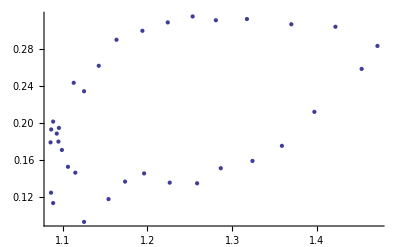

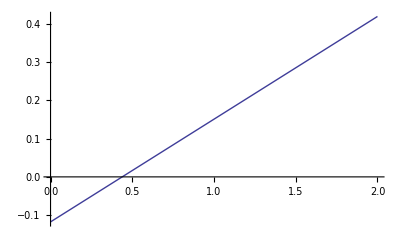

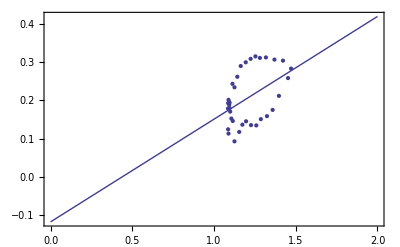

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```